# Función Espectral de Fourier - Iván Josué Arreola Silva

## Función espectral de Fourier en el análisis de datos

# Un espectro de frecuencias es aplicado para obtener la distribución de amplitudes en cada frecuencia, para este caso se aplicará la función espectral llamada “espectro de Fourier” en las anomalías de temperatura media anual de la Tierra.

# Cambio medio anual de la temperatura del aire en la superficie global

# A partir de los datos de anomalías de la temperatura media anual de la superficie de la Tierra, tomados de la página de la NASA llamada “Goddard Institute for Space Studies” (GISS, por sus siglas en ingles) para los últimos 80 años (1939 a 2018), para ello primero se importa la base de datos contenida en un archivo .csv de Excel con el código “Import”, para después con el código “DateListPlot” se obtienen las siguientes gráficas para los datos no suavizados y suavizados respectivamente.

```mathematica
Import["temperatura.csv"]//Short; Import["t.csv"]//Short
```

{{1939,0.03},{1940,0.06},{1941,0.09},{1942,0.1},{1943,0.1},{1944,0.07},«68»,{2013,0.74},{2014,0.78},{2015,0.83},{2016,0.87},{2017,0.91},{2018,0.96}}

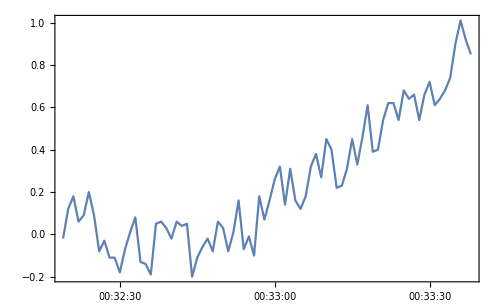

```mathematica
DateListPlot[Import["temperatura.csv"]]
```

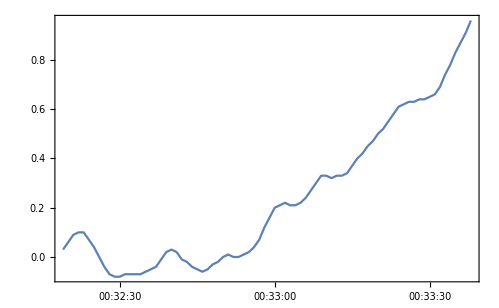

```mathematica
DateListPlot[Import["t.csv"]]
```

# Se observa que en la segunda gráfica (abajo) para la base de datos suavizada, hay 5 picos en la anomalía de la temperatura de los años 1943 con 0.09°C, 1961 con 0.06°C, 1981 con 0.32°C, 1990 con 0.45°C y 2010 con 0.72°C, esto al dar clic derecho sobre las gráficas y seleccionando la opción “Obtener coordenadas” nos indica en cualquier punto de la gráfica la anomalía de la temperatura en su respectivo año, el código está disponible en: Ahora por el espectro de Fourier con el uso del código “ListLinePlot” con el comando “Abs” para valores absolutos y el comando “Fourier” para obtener la transformada de Fourier discreta, aplicado a las 2 bases de datos antes graficadas se tiene lo siguiente:

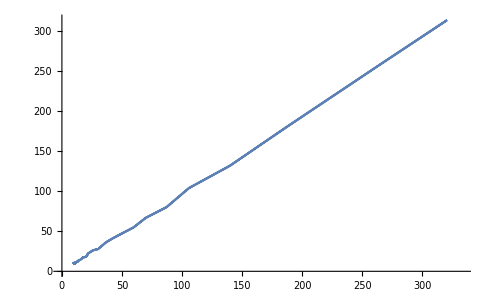

```mathematica
ListLinePlot[Abs[Fourier[Import["temperatura.csv"]]]^2]
```

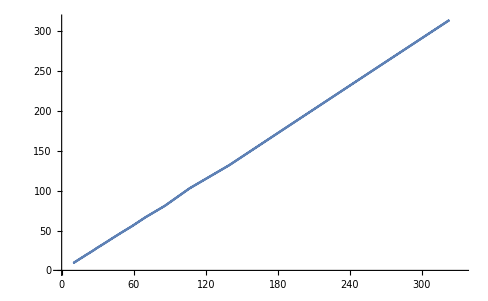

```mathematica
ListLinePlot[Abs[Fourier[Import["t.csv"]]]^2]
```

# Se observa que la transformada de Fourier para la base de datos no suavizada y suavizada describe un incremento lineal, donde para la segunda es más marcada que la primera, por lo que la anomalía de la temperatura media global va en incremento desde los últimos 80 años. FUENTES National Aeronautics and Space Administration, Goddard Institute for Space Studies (2019). GISS Surface Temperature Analysis (v4). GISS, NASA. Recuperado de: https://data.giss.nasa.gov/gistemp/graphs_v4/# Wolfram Language & System Documentation Center (2012). Fourier. Wolfram Mathematica Documention Center. Recuperado de: https://reference.wolfram.com/language/ref/Fourier.html